```mathematica
Manipulate[
p = Exp[alpha + beta*Log[PreyMass/PredMass] + gamma*Log[PreyMass/PredMass]^2];
prob = p/(1+p);
Plot[prob,{PreyMass,0,1000},PlotRange->{0,1}],
{{PredMass,50},1,1000},
{{alpha,-0.43},-4,4},
{{beta,-4},-10,4},
{{gamma,-2.14},-4,4}]
```

```mathematica
α = -1.77
β = -8.54
γ = -3.33
```

-1.77

-8.54

-3.33

```mathematica
bodysize = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/bodysizedata.csv","Data"];
fmatrix = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/foraging_matrix.csv","Data"];
```

```mathematica
BMmin = Delete[bodysize[[All,2]],1];
BMmax = Delete[bodysize[[All,3]],1];
BMavg = N[Mean[{BMmin,BMmax}]];
fwsize = Length[BMavg];
```

```mathematica
Spp = Delete[fmatrix[[1,All]],1];
```

```mathematica
f = fmatrix[[2;;fwsize+1,2;;fwsize+1]];
```

```mathematica
PRint = Table[
p = Exp[α + β*Log[BMavg[[j]]/BMavg[[i]]] + γ*Log[BMavg[[j]]/BMavg[[i]]]^2 + f[[i,j]]];
p/(1+p),
{i,1,fwsize},
{j,1,fwsize}
];
```

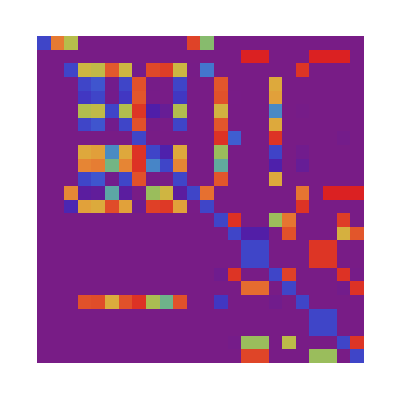

```mathematica
ArrayPlot[PRint,ColorFunction->"Rainbow"]
```

```mathematica
PRint[[2,All]]
```

{2.53552×10^-47,6.33652×10^-45,7.92343×10^-43,9.76809×10^-53,6.23018×10^-53,1.45771×10^-50,9.76809×10^-53,9.40181×10^-59,7.32969×10^-50,2.96437×10^-49,9.76809×10^-53,1.49832×10^-42,6.26811×10^-43,1.6571×10^-72,1.95872×10^-92,1.,1.,4.16187×10^-76,6.63712×10^-105,4.13756×10^-48,1.,1.,1.,7.22424×10^-130}

{{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,0},{0,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

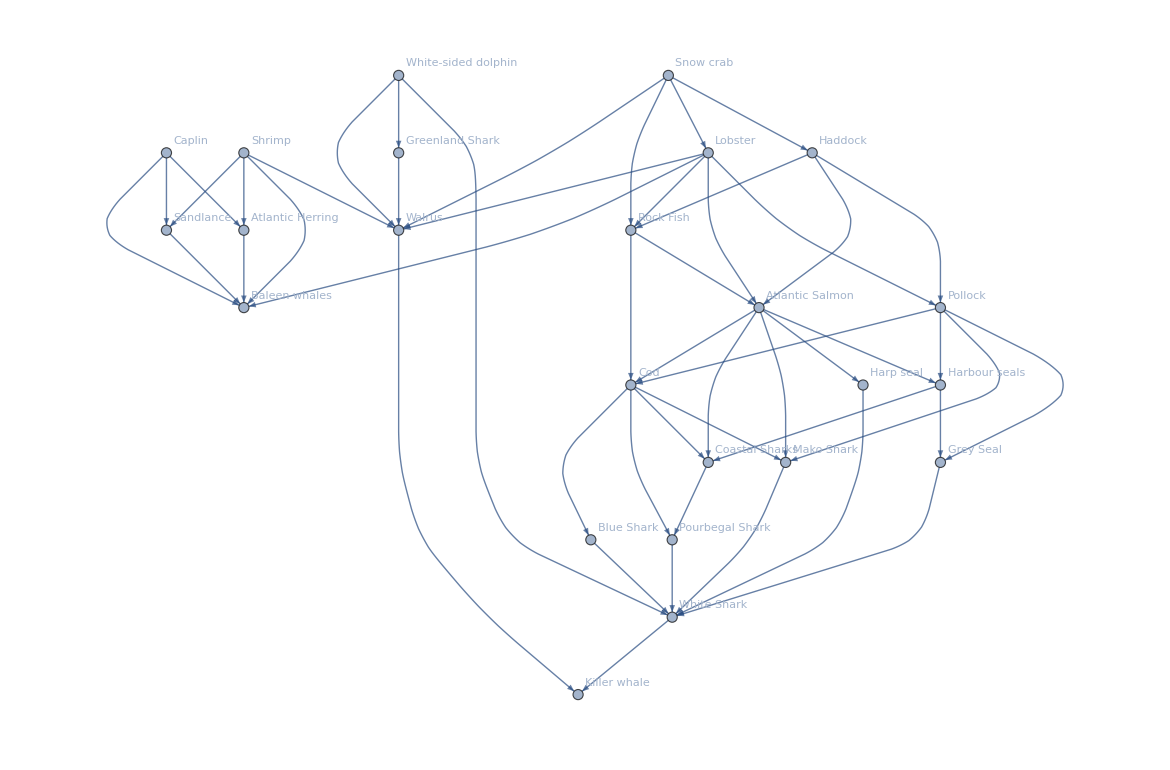

```mathematica
fw = Table[
If[i<j,
rv = RandomReal[];
If[
rv < PRint[[i,j]],
1,0],
0],
{i,1,fwsize},
{j,1,fwsize}
]
AdjacencyGraph[
Transpose[fw],VertexLabels->Table[i->Spp[[i]],{i,1,fwsize}]]
```